# An Uncharted Method: Label Regularizations

### Load CIFAR-100

```mathematica
resource=ResourceObject["CIFAR-100"];
```

```mathematica
trainingData=ResourceData[resource,"TrainingData"];
testData=ResourceData[resource,"TestData"];

Length[trainingData]
Length[testData]
```

50000

10000

```mathematica
RandomSample[trainingData, 5]
```

{-Graphics-→elephant,-Graphics-→ray,-Graphics-→snail,-Graphics-→cockroach,-Graphics-→forest}

#### Since we are conducting a Single Task Object Classification, we use sublabels as the main label.

https://www.wolfram.com/language/11/neural-networks/object-classification.html.ko?product=language

```mathematica
classes=Union@Values[trainingData]
Length[classes]
```

{apple,aquarium fish,baby,bear,beaver,bed,bee,beetle,bicycle,bottle,bowl,boy,bridge,bus,butterfly,camel,can,castle,caterpillar,cattle,chair,chimpanzee,clock,cloud,cockroach,computer keyboard,couch,crab,crocodile,cup,dinosaur,dolphin,elephant,flatfish,forest,fox,girl,hamster,house,kangaroo,lamp,lawn-mower,leopard,lion,lizard,lobster,man,maple tree,motorcycle,mountain,mouse,mushroom,oak tree,orange,orchid,otter,palm tree,pear,pickup truck,pine tree,plain,plate,poppy,porcupine,possum,rabbit,raccoon,ray,road,rocket,rose,sea,seal,shark,shrew,skunk,skyscraper,snail,snake,spider,squirrel,streetcar,sunflower,sweet pepper,table,tank,telephone,television,tiger,tractor,train,trout,tulip,turtle,wardrobe,whale,willow tree,wolf,woman,worm}

100

### Set up a CNN

#### Define a simple CNN that takes 32x32 images as input (VGG-style cnn)

```mathematica
cifarNet=NetChain[
{
(*
ImageAugmentationLayer[ (* Data Augmentation *)
{
"RandomReflection"->True,
"RandomResizedCrop"->{32, 32, 0.8},
"RandomRotation"->{-10, 10}
}
], 
*)
(* convolution block 1*)
ConvolutionLayer[64, 3, "PaddingSize"->1], (* 3x3 convolutions *)
Ramp,
BatchNormalizationLayer[],
PoolingLayer[2, 2], (* 차원 감소 효과 *) (* 32 -> 16 *)
(* conv block 2 *)
ConvolutionLayer[128, 3, "PaddingSize"->1],
Ramp,
BatchNormalizationLayer[],
PoolingLayer[2, 2], (* 16 -> 8 *)
(* conv block 3 *)
ConvolutionLayer[256, 3, "PaddingSize"->1],
Ramp,
BatchNormalizationLayer[],
PoolingLayer[2, 2], (* 8 -> 4 *)

FlattenLayer[],

LinearLayer[512],
Ramp,
BatchNormalizationLayer[],
(*DropoutLayer[0.5], *)

LinearLayer[100],
SoftmaxLayer[]
},
"Output"->NetDecoder[{"Class", classes}],
"Input"->NetEncoder[{"Image", {32,32}}]
]
```

NetChain[…]

- Filter counts (64 -> 128 -> 256) and 512-unit dense layer are typical for CIFAR-sized images. 
- Regularization: BatchNormalizationLayer[] and DropoutLayer[0.5]
- Augmentation: ImageAugmentationLayer[] (excluded due to error)
- Preprocessing: NetEncoder[]

#### Train the network for 5 training rounds.

```mathematica
net=NetTrain[
cifarNet,
trainingData,
ValidationSet->Scaled[0.1],
BatchSize->128,
MaxTrainingRounds->5
]
trained=results["TrainedNet"]
```

NetChain[<18>]

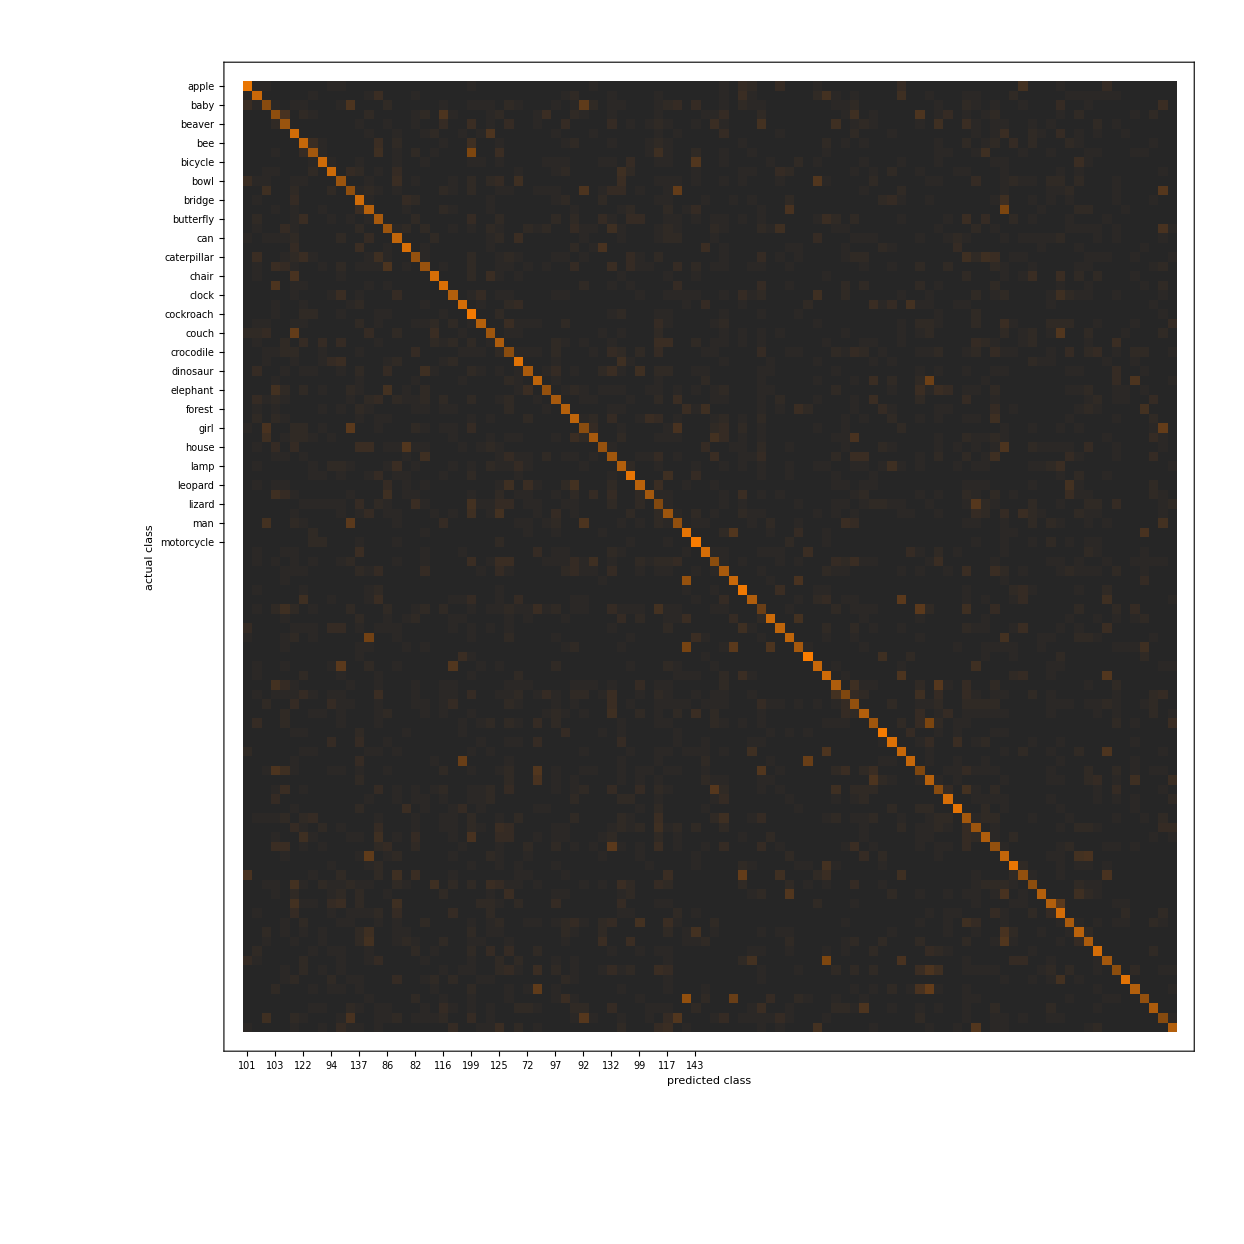
Classifier Measurements
Classifier method | Net
Number of test examples | 10000
Accuracy | (45.50.5) %
Accuracy baseline | (1.000.10) %
Geometric mean of probabilities | 0.0855 ± 0.0023
Mean cross entropy | 2.46 ± 0.027
Single evaluation time | 3.5 ms/example
Batch evaluation speed | 1.14 examples/ms
-Graphics- |

```mathematica
cm = ClassifierMeasurements[net, testData];
cm["Report"]
```